# DescendingSublists

DescendingSublists[list]
makes sublists of list starting at its left-to-right maxima.

The elements in the sublists are in the same order as the original list.

A left-to-right maximum is greater than any preceding element.

The first element of each sublist is its maximum.

The first elements of the sublists are increasing.

## See AlsoSeeAlsoInsert links to any related reference (function) pages.

Cycles ▪ PermutationList ▪

## Tech NotesTechNotesInsert links to related tech notes.

## Related Guides

## Related LinksRelatedLinksInsert links to any related page, including web pages.

## Examples InitializationExamplesInitializationInput that is to be evaluated before any examples are run, e.g. Needs[…].

```mathematica
Needs["PeterBurbery`Combinatorics`"]
```

## Basic Examples | More Examples ⊳

Split a permutation given as a list into sublists starting at its left-to-right maximum:

```mathematica
DescendingSublists@{2,4,1,6,7,5,3}
```

{{2},{4,1},{6},{7,5,3}}

The input does not have to be a permutation:

```mathematica
r1=RandomInteger[{1,7},20]
```

{1,2,3,2,6,4,7,7,5,3,6,6,6,6,4,1,7,7,5,6}

```mathematica
DescendingSublists@r1
```

{{1},{2},{3,2},{6,4},{7,7,5,3,6,6,6,6,4,1,7,7,5,6}}

Flatten to get back the original list:

```mathematica
r1==Flatten@%
```

True

## More ExamplesMoreExamplesExtended examples in standardized sections.

### Scope

Here is a larger example:

```mathematica
p1=PermutationList@RandomPermutation@50
```

{7,19,31,9,12,27,42,10,39,25,26,16,8,34,5,15,47,11,32,40,3,18,48,50,21,35,46,30,29,36,45,43,22,1,33,24,20,14,37,44,28,41,2,49,6,4,38,17,13,23}

```mathematica
s1=DescendingSublists@p1
```

{{7},{19},{31,9,12,27},{42,10,39,25,26,16,8,34,5,15},{47,11,32,40,3,18},{48},{50,21,35,46,30,29,36,45,43,22,1,33,24,20,14,37,44,28,41,2,49,6,4,38,17,13,23}}

Each sublist starts from its maximum:

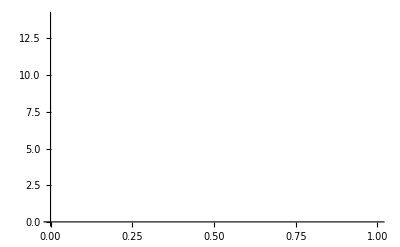
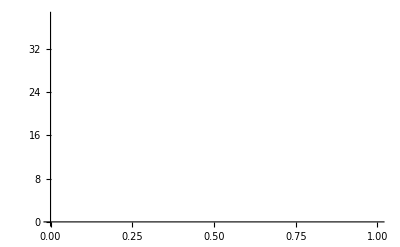
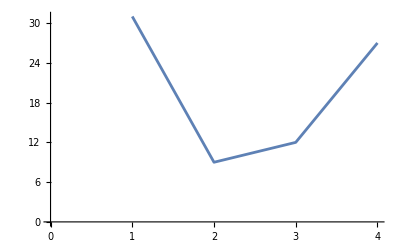
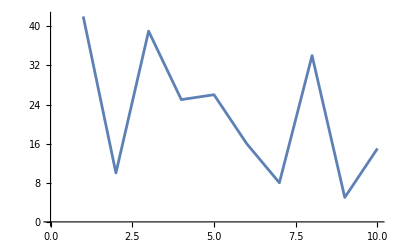
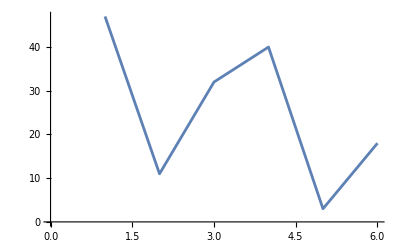
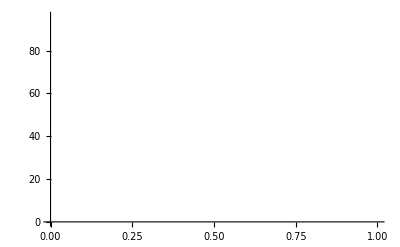
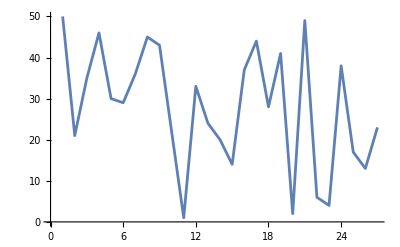

```mathematica
Row[ListLinePlot/@s1]
```

The first elements are increasing:

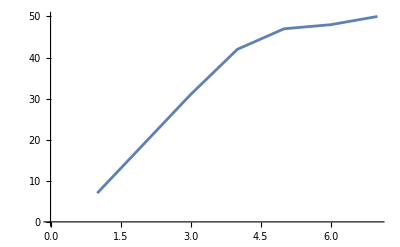

```mathematica
ListLinePlot[First/@s1]
```

The sublists of s1 an be thought of as cycle notation for the permutation, but with a different canonical form than the Wolfram Language default, where each sublist starts with its minimum:

```mathematica
Cycles[s1]
```

Cycles[{{1,14,44,19,21,37,3,10,48,32,4,47,33,8,26,24,39,31,5,49},{2,20,16,17,36,50,28,43,35,18,6,41,9,11,40},{7,25,23,38,30,42,45,34},{12,27,29,15,46},{13,22}}]

### Generalizations & Extensions

### Options

### Applications

### Properties & Relations

### Possible Issues

### Interactive Examples

### Neat Examples

## Metadata

### CategorizationMetadataMetadata such as page URI, context, and type of documentation page.

Symbol

PeterBurbery/Combinatorics

PeterBurbery`Combinatorics`

PeterBurbery/Combinatorics/ref/DescendingSublists

### Keywords

### Syntax Templates